## Panel Plot for sensitivity of trajectories - varying kappa, delta and beta

## Import Data

```mathematica
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
rawKappaLow=Import["export_data/sensi_anal/kappa_low.mat"];
rawKappaHigh=Import["export_data/sensi_anal/kappa_high.mat"];

rawDeltaLow=Import["export_data/sensi_anal/delta_low.mat"];
rawDeltaHigh=Import["export_data/sensi_anal/delta_high.mat"];

rawBetaLow=Import["export_data/sensi_anal/beta_low.mat"];
rawBetaHigh=Import["export_data/sensi_anal/beta_high.mat"];
```

## Image Options

```mathematica
(* time ticks *)
timeTicks=Table[{50(i-1),1800+50(i-1)},{i,1,13}];

(* imgs size *)
imgs=300;
(* aspect ratio *)
aratio=0.8;
(* legend position (scaled) *)
legendPos={0.2,0.7};
(* labels (alphabet) *)
labels=Alphabet[];
(* label position (scaled) *)
labelPos={0.05,0.91};
(* bold label on off *)
bold=1;
```

```mathematica
{padLeft,padRight,padBottom,padTop}={50,30,40,20};  (* image padding *)
```

```mathematica
(* time plot range *)
plRange={100,400};
(* social plot range *)
plRangeSoc={-0.02,1.05};
(* emissions plot range *)
plRangeEm={-0.5,18.5};
(* temperature plot range *)
plRangeTemp={-0.1,5.3};
```

```mathematica
(* varying parameter values *)
deltaVals={0,0.5,1,1.5,2,3};
kappaVals={0.01,0.02,0.05,0.1,0.2,100};
```

```mathematica
(* colour of shading *)
shade1=Directive[Opacity[0.5],Lighter[TMBcolours⟦1⟧,0.8]];
shade2=Directive[Opacity[0.5],Lighter[TMBcolours⟦3⟧,0.8]];
```

```mathematica
(* generic plot options *)
opts={PlotStyle->{TMBcolours⟦1⟧,shade1,shade1,TMBcolours⟦3⟧,shade2,shade2},
Filling->{2->{{1},shade1},
3->{{1},shade1},
5->{{4},shade2},
6->{{4},shade2}},
FrameTicks->{{Automatic,None},{timeTicks,None}},
ImageSize->imgs,
AspectRatio->aratio,
Frame->True,
LabelStyle->14,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}};
```

## Kappa Plots

### Break up data

```mathematica
(* kappa lower bound *)
tSeriesKL = rawKappaLow[[1,1]];
socSeriesKL = rawKappaLow[[1,2;;]];
emissionSeriesKL=rawKappaLow[[2,2;;]];
tempSeriesKL=rawKappaLow[[3,2;;]];

(* kappa upper bound *)
tSeriesKU = rawKappaHigh[[1,1]];
socSeriesKU = rawKappaHigh[[1,2;;]];
emissionSeriesKU=rawKappaHigh[[2,2;;]];
tempSeriesKU=rawKappaHigh[[3,2;;]];
```

### Make Plots

```mathematica
legendKappa=LineLegend[Table[TMBcolours[[i]],{i,{1,3}}],{"κ=0.02","κ=0.2"}]
```

```mathematica
(* proportion of mitigators *)
socPlotKappa=ListLinePlot[{Transpose[{tSeries,socSeriesKL[[2]]}],
Transpose[{tSeries,socSeriesKL[[1]]}],
Transpose[{tSeries,socSeriesKL[[3]]}],
Transpose[{tSeries,socSeriesKU[[2]]}],
Transpose[{tSeries,socSeriesKU[[1]]}],
Transpose[{tSeries,socSeriesKU[[3]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[1]],14,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"Proportion of mitigators",None},{None,None}},
PlotLegends->Placed[legendKappa,Scaled[legendPos]]];
```

```mathematica
(* emissions *)
emissionPlotKappa=ListLinePlot[{Transpose[{tSeries,emissionSeriesKL[[2]]}],
Transpose[{tSeries,emissionSeriesKL[[1]]}],
Transpose[{tSeries,emissionSeriesKL[[3]]}],
Transpose[{tSeries,emissionSeriesKU[[2]]}],
Transpose[{tSeries,emissionSeriesKU[[1]]}],
Transpose[{tSeries,emissionSeriesKU[[3]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[2]],14,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"CO_2emissions (gtC yr^-1)",None},{None,None}}];
```

```mathematica
(* temperature plot *)
tempPlotKappa=ListLinePlot[{Transpose[{tSeries,tempSeriesKL[[2]]}],
Transpose[{tSeries,tempSeriesKL[[1]]}],
Transpose[{tSeries,tempSeriesKL[[3]]}],
Transpose[{tSeries,tempSeriesKU[[2]]}],
Transpose[{tSeries,tempSeriesKU[[1]]}],
Transpose[{tSeries,tempSeriesKU[[3]]}]},
PlotRange->{plRange,{0,5}},
opts,
Epilog->Text[Style[labels[[3]],14,If[bold==1,Bold]],Scaled[labelPos]],
FrameLabel->{{"Temperature change (°C)",None},{"Year",None}}];
```

## Delta Plots

### Break up data

```mathematica
(* kappa lower bound *)
tSeries = rawDeltaLow[[1,1]];
socSeriesDL = rawDeltaLow[[1,2;;]];
emissionSeriesDL=rawDeltaLow[[2,2;;]];
tempSeriesDL=rawDeltaLow[[3,2;;]];

(* kappa upper bound *)
socSeriesDU = rawDeltaHigh[[1,2;;]];
emissionSeriesDU=rawDeltaHigh[[2,2;;]];
tempSeriesDU=rawDeltaHigh[[3,2;;]];
```

### Make Plots

```mathematica
legendDelta=LineLegend[Table[TMBcolours[[i]],{i,{1,3}}],{"δ=0.5","δ=1.5"}];
```

```mathematica
(* proportion of mitigators *)
socPlotDelta=ListLinePlot[{Transpose[{tSeries,socSeriesDL[[2]]}],
Transpose[{tSeries,socSeriesDL[[1]]}],
Transpose[{tSeries,socSeriesDL[[3]]}],
Transpose[{tSeries,socSeriesDU[[2]]}],
Transpose[{tSeries,socSeriesDU[[1]]}],
Transpose[{tSeries,socSeriesDU[[3]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[4]],14,If[bold==1,Bold]],Scaled[labelPos]],
PlotLegends->Placed[legendDelta,Scaled[legendPos]]];
```

```mathematica
(* emissions *)
emissionPlotDelta=ListLinePlot[{Transpose[{tSeries,emissionSeriesDL[[2]]}],
Transpose[{tSeries,emissionSeriesDL[[1]]}],
Transpose[{tSeries,emissionSeriesDL[[3]]}],
Transpose[{tSeries,emissionSeriesDU[[2]]}],
Transpose[{tSeries,emissionSeriesDU[[1]]}],
Transpose[{tSeries,emissionSeriesDU[[3]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[5]],14,If[bold==1,Bold]],Scaled[labelPos]]];
```

```mathematica
(* temperature plot *)
tempPlotDelta=ListLinePlot[{Transpose[{tSeries,tempSeriesDL[[2]]}],
Transpose[{tSeries,tempSeriesDL[[1]]}],
Transpose[{tSeries,tempSeriesDL[[3]]}],
Transpose[{tSeries,tempSeriesDU[[2]]}],
Transpose[{tSeries,tempSeriesDU[[1]]}],
Transpose[{tSeries,tempSeriesDU[[3]]}]},
PlotRange->{plRange,{0,5}},
opts,
Epilog->Text[Style[labels[[6]],14,If[bold==1,Bold]],Scaled[labelPos]]];
```

## Beta Plots

### Break up data

```mathematica
(* beta lower bound *)
tSeries = rawBetaLow[[1,1]];
socSeriesBL = rawBetaLow[[1,2;;]];
emissionSeriesBL=rawBetaLow[[2,2;;]];
tempSeriesBL=rawBetaLow[[3,2;;]];

(* beta upper bound *)
socSeriesBU = rawBetaHigh[[1,2;;]];
emissionSeriesBU=rawBetaHigh[[2,2;;]];
tempSeriesBU=rawBetaHigh[[3,2;;]];
```

### Make Plots

```mathematica
legendBeta=LineLegend[Table[TMBcolours[[i]],{i,{1,3}}],{"β=0.5","β=1.5"}]
```

```mathematica
(* proportion of mitigators *)
socPlotBeta=ListLinePlot[{Transpose[{tSeries,socSeriesBL[[2]]}],
Transpose[{tSeries,socSeriesBL[[1]]}],
Transpose[{tSeries,socSeriesBL[[3]]}],
Transpose[{tSeries,socSeriesBU[[2]]}],
Transpose[{tSeries,socSeriesBU[[1]]}],
Transpose[{tSeries,socSeriesBU[[3]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[7]],14,If[bold==1,Bold]],Scaled[labelPos]],
PlotLegends->Placed[legendBeta,Scaled[legendPos]]];
```

```mathematica
(* emissions *)
emissionPlotBeta=ListLinePlot[{Transpose[{tSeries,emissionSeriesBL[[2]]}],
Transpose[{tSeries,emissionSeriesBL[[1]]}],
Transpose[{tSeries,emissionSeriesBL[[3]]}],
Transpose[{tSeries,emissionSeriesBU[[2]]}],
Transpose[{tSeries,emissionSeriesBU[[1]]}],
Transpose[{tSeries,emissionSeriesBU[[3]]}]},
PlotRange->{plRange,All},
opts,
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->Text[Style[labels[[8]],14,If[bold==1,Bold]],Scaled[labelPos]]];
```

```mathematica
(* temperature plot *)
tempPlotBeta=ListLinePlot[{Transpose[{tSeries,tempSeriesBL[[2]]}],
Transpose[{tSeries,tempSeriesBL[[1]]}],
Transpose[{tSeries,tempSeriesBL[[3]]}],
Transpose[{tSeries,tempSeriesBU[[2]]}],
Transpose[{tSeries,tempSeriesBU[[1]]}],
Transpose[{tSeries,tempSeriesBU[[3]]}]},
PlotRange->{plRange,{0,5}},
opts,
Epilog->Text[Style[labels[[9]],14,If[bold==1,Bold]],Scaled[labelPos]]];
```

## Plot Grid

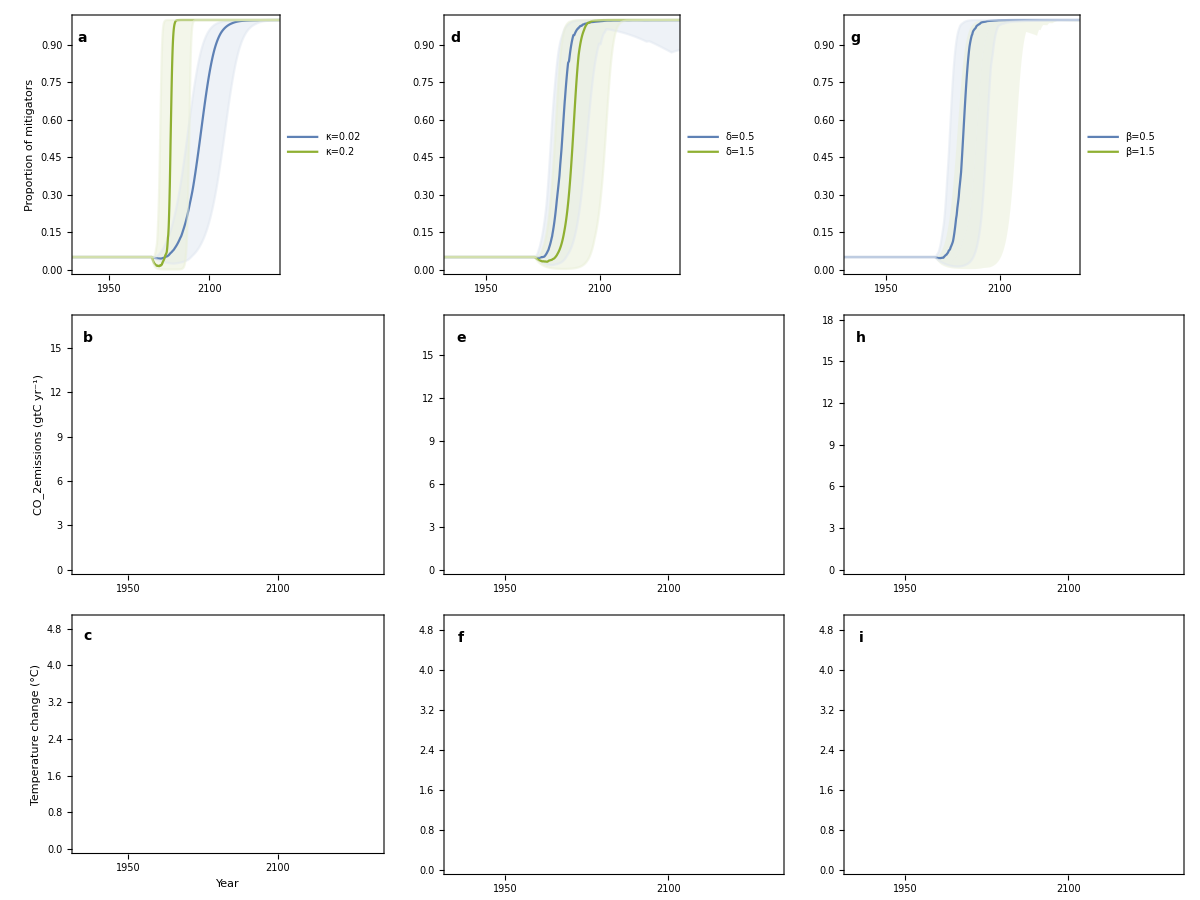

```mathematica
plotGrid=Grid[{{socPlotKappa,socPlotDelta,socPlotBeta},{emissionPlotKappa,emissionPlotDelta,emissionPlotBeta},{tempPlotKappa,tempPlotDelta,tempPlotBeta}},Spacings->{-2.4,-2.2}]
```

```mathematica
Export["figures/sensi_delta_kappa_beta.png",plotGrid,ImageResolution->200];
```